## Test different dithering distributions (Problem 5.2)

```mathematica
Clear["Global`*"];
```

Uniform dither

```mathematica
Integrate[Round[x0+ξ] ,{ξ,-1/2,1/2}, Assumptions -> 0<x0<1]
```

x0

```mathematica
Integrate[(Round[x0+ξ]-x0)^2,{ξ,-1/2,1/2}, Assumptions -> 0<x0<1]
```

x0-x0^2

```mathematica
(* for uniform noise, <x> = x0 (no bias) but Var = x0(1-x0) -> depends on x0, which is no good *)
```

Triangular dither

```mathematica
Integrate[Round[x0+ξ] (1-Abs[ξ]),{ξ,-1,1}, Assumptions -> 0<x0<1]
```

Piecewise[{{x0, 0<x0<1/2||1/2<x0<1}, {1/8 (1+4 x0+4 x0^2), True}}]

```mathematica
Integrate[(Round[x0+ξ]-x0)^2(1-Abs[ξ]),{ξ,-1,1}, Assumptions -> 0<x0<1]
```

Piecewise[{{1/4, 0<x0<1/2||1/2<x0<1}, {1/8 (3+2 x0-7 x0^2-4 x0^3+4 x0^4), True}}]

```mathematica
(* for triangular noise <x> = x0 (no bias) and Var = 1/4,independent of x0 *)
```

Gaussian Noise (normal distribution)

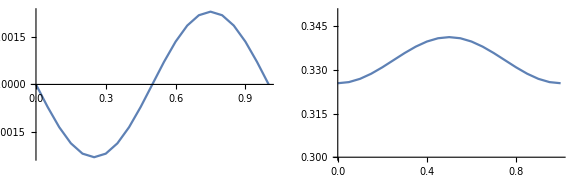

```mathematica
p1=DiscretePlot[NIntegrate[Round[x0+ξ] PDF[NormalDistribution[0,1/2],ξ],{ξ,-3,3},AccuracyGoal->8]-x0,{x0,0,1,0.05},Filling->None,Joined->True];
p2=DiscretePlot[NIntegrate[(Round[x0+ξ]-x0)^2 PDF[NormalDistribution[0,1/2],ξ],{ξ,-3,3}],{x0,0,1,0.05},PlotRange->{0.3,0.35},Filling->None,Joined->True];
GraphicsRow[{p1,p2},ImageSize->Large]
```

```mathematica
(* Adding Gaussian noise gives mean ~x0 and variance roughly independent of x0 -- but not quite *)
```

Subtractive dither (with uniform noise)

```mathematica
Integrate[Round[x0+ξ] -ξ,{ξ,-1/2,1/2}, Assumptions -> 0<x0<1]
```

x0

```mathematica
Integrate[(Round[x0+ξ]-ξ-x0)^2,{ξ,-1/2,1/2}, Assumptions -> 0<x0<1]
```

1/12

```mathematica
Sqrt[%]//N
```

0.288675

```mathematica
(* Subtractive dither is best but harder to implement *)
```